```mathematica
<<getFeigenbaum`
f[r_,x_]:=1-r*x^2;
rInv={0,2};
a=getScalingFactor[f,rInv,4];
r=Drop[getSuperstablePoints[f,rInv,4],1];
```

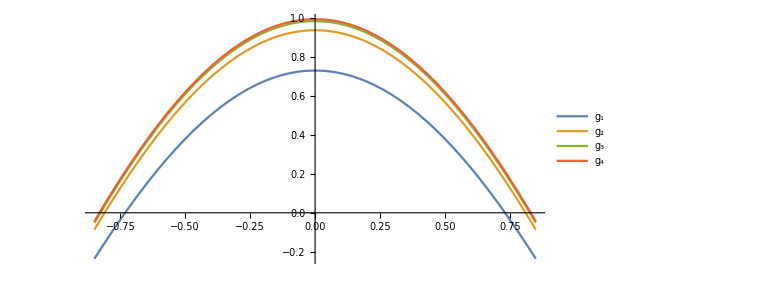

```mathematica
(* visualize the convergence of g_r *)
fn[x_,n_,k_]:=(-a)^n*Nest[f[r[[k]],#]&,x/(-a)^n,2^n];
Plot[Evaluate[Table[fn[x,7,7+k],{k,1,4}]],{x,-0.85,0.85},PlotStyle->Opacity[1],AspectRatio->1/2,PlotLegends->Placed[{"g_1","g_2","g_3","g_4"},{0.95,0.75}],ImageSize->Large]
```

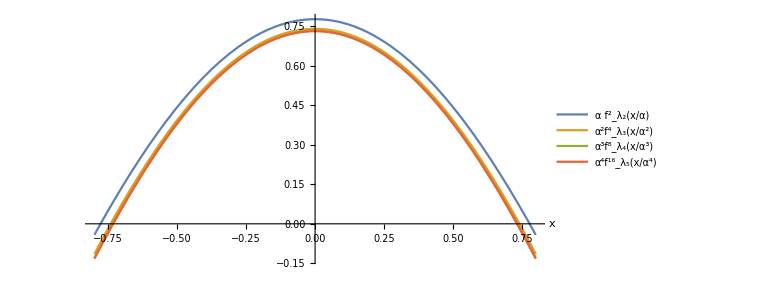

```mathematica
(* visualize the convergence to g_1 *)
fn[x_,n_]:=(-a)^n*Nest[f[r[[n+1]],#]&,x/(-a)^n,2^n];
Plot[Evaluate[Table[fn[x,n],{n,1,4}]],{x,-0.8,0.8},ImageSize->Large,AspectRatio->1/2,
AxesLabel->{x},PlotLegends->Placed[{"α (f^2)_λ_2(x/α)","α^2(f^4)_λ_3(x/α^2)","α^3(f^8)_λ_4(x/α^3)","α^4(f^16)_λ_5(x/α^4)"},{0.635,0.41}]]
```

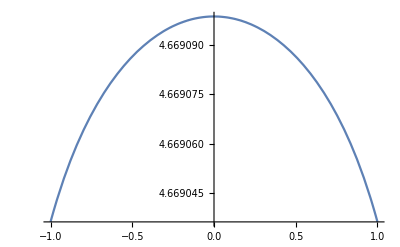

```mathematica
(* Plot the ratio of the successive pointwise ratio of the functions g_r *)
getDelta[x_,n_,k_]:=(fn[x,n,n+k]-fn[x,n,n+1+k])/(fn[x,n,n+1+k]-fn[x,n,n+2+k]);
Plot[getDelta[x,3,6],{x,-1,1}]
```